```mathematica
mudis=Import["/home/gstenico/Desktop/nu-LED-2/ev-rates/nu-mu-dis-larnd-no.dat","Data"];
mudis2=Import["/home/gstenico/Desktop/nu-LED-2/ev-rates/nu-mu-dis-ICARUS-no.dat","Data"];
```

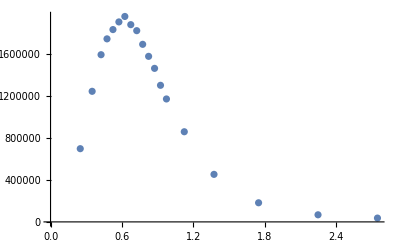

```mathematica
ListPlot[Table[{murate[[i,1]],mudis[[i,2]]},{i,1,Length[mudis]}]]
```

```mathematica
Sum[mudis[[i,2]]*murate[[i,2]],{i,1,Length[mudis]}]/Sum[murate[[i,3]],{i,1,Length[mudis]}]
```

1.00511

```mathematica
murate=Import["/home/gstenico/Downloads/GLOBES/globes-3.2.17/SBND/sig-bg-SBND/lar-m-sig.dat","Data"];
murate2=Import["/home/gstenico/Downloads/GLOBES/globes-3.2.17/SBND/sig-bg-SBND/ic-m-sig.dat","Data"];
```

```mathematica
Table[1/murate[[i,2]],{i,1,Length[murate]}]
```

{10.,10.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,20.,4.,4.,2.,2.,2.}

```mathematica
murate
```

{{0.25,0.1,392489,2009.41},{0.35,0.1,900921,4082.57},{0.425,0.05,672171,2930.9},{0.475,0.05,830631,3533.12},{0.525,0.05,989900,4107.97},{0.575,0.05,1.1407×10^6,4617.68},{0.625,0.05,1.26958×10^6,5031.21},{0.675,0.05,1.36289×10^6,5306.08},{0.725,0.05,1.4318×10^6,5494.77},{0.775,0.05,1.48689×10^6,5642.03},{0.825,0.05,1.49669×10^6,5628.33},{0.875,0.05,1.48062×10^6,5526.97},{0.925,0.05,1.45441×10^6,5396.76},{0.975,0.05,1.38846×10^6,5127.03},{1.125,0.25,5.69287×10^6,20816.1},{1.375,0.25,3.54034×10^6,12763.2},{1.75,0.5,3.1755×10^6,11305.2},{2.25,0.5,1.14424×10^6,4032.03},{2.75,0.5,689438,2397.24}}

```mathematica
Table[((mudis[[i,2]]*murate[[i,2]])/(murate[[i,3]])),{i,1,Length[mudis]}]
```

{0.168684,0.134205,0.116093,0.103341,0.0916223,0.0831809,0.0771912,0.068994,0.0636922,0.0574041,0.0530515,0.0496703,0.0453315,0.0425757,0.0379051,0.0319058,0.028431,0.029067,0.0262853}

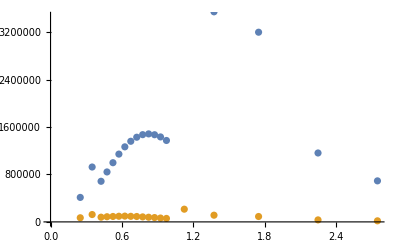

```mathematica
ListPlot[{Table[{murate[[i,1]],murate[[i,3]]},{i,1,Length[murate]}],Table[{murate[[i,1]],mudis[[i,2]]*murate[[i,2]]},{i,1,Length[murate]}]}]
```

```mathematica
NMinimize[Sum[(1/1000)((1+a+b)*murate[[i,3]]-mudis[[i,2]]*murate[[i,2]])^2/(mudis[[i,2]]*murate[[i,2]])+(1/1000)((1+a+b)*murate2[[i,3]]-mudis2[[i,2]]*murate2[[i,2]])^2/(mudis2[[i,2]]*murate2[[i,2]]),{i,1,Length[murate]}]+(a/0.1)^2+(b/0.01)^2,{a,b}]
```

{0.0565111,{a→0.00424325,b→0.0000424325}}

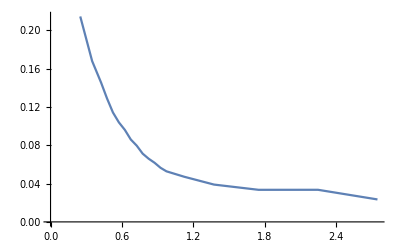

```mathematica
ListPlot[Table[{murate[[i,1]],(mudis[[i,2]]*murate[[i,2]])/(murate[[i,3]])},{i,1,Length[mudis]}],Joined->True]
```

```mathematica
murate2=Import["/home/gstenico/Downloads/GLOBES/globes-3.2.17/SBND/ev-mm-lar.dat","Data"];
```

```mathematica
murate2
```

{{0.25,0.1,69091.1,4489.55},{0.35,0.1,122597,7020.73},{0.425,0.05,78960.9,4330.44},{0.475,0.05,86233.7,4604.32},{0.525,0.05,90649.3,4717.19},{0.575,0.05,94545.2,4801.66},{0.625,0.05,96882.7,4817.22},{0.675,0.05,93246.6,4555.06},{0.725,0.05,90649.3,4364.6},{0.775,0.05,83636.6,3980.65},{0.825,0.05,78181.5,3686.65},{0.875,0.05,72467.5,3391.44},{0.925,0.05,64675.2,3008.13},{0.975,0.05,57922.3,0},{1.125,0.25,212987,0},{1.375,0.25,110390,0},{1.75,0.5,85714.3,0},{2.25,0.5,31168.8,0},{2.75,0.5,12987,0}}

```mathematica
Table[{murate2[[i,1]],(murate2[[i,3]]/murate2[[i,2]])},{i,1,Length[murate2]}]
```

{{0.25,83290.7},{0.35,137789.},{0.425,176864.},{0.475,193316.},{0.525,212854.},{0.575,225194.},{0.625,234448.},{0.675,239588.},{0.725,241646.},{0.775,245758.},{0.825,235476.},{0.875,230334.},{0.925,224164.},{0.975,212854.},{1.125,175835.},{1.375,108997.},{1.75,42159.4},{2.25,10282.8},{2.75,4113.12}}

```mathematica
mudis
```

```mathematica
murate3=Import["/home/gstenico/Downloads/GLOBES/globes-3.2.17/SBN/ev-rat-nu-mu.dat","Data"];
```

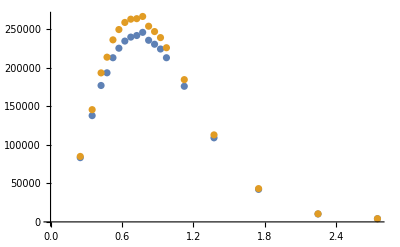

```mathematica
ListPlot[{Table[{murate2[[i,1]],murate2[[i,3]]/murate2[[i,2]]},{i,1,Length[murate2]}],Table[{murate3[[i,1]],murate3[[i,3]]/murate3[[i,2]]},{i,1,Length[murate3]}]}]
```

```mathematica
eapp=Import["/home/gstenico/Desktop/nu-LED-2/ev-rates/nu-e-app-sig-LAR.dat","Data"];
```

```mathematica
eappc=Table[{eapp[[i,1]],(eapp[[i+1,2]]-eapp[[i,2]])},{i,1,Length[eapp],2}];
```

```mathematica
eappc
```

{{0.27875,155.039},{0.42408,258.398},{0.577637,258.398},{0.722461,103.359},{0.879883,51.6796},{1.02463,51.6796},{1.19902,51.6796},{1.39906,51.6796},{1.62473,51.6796},{1.8758,51.6796},{2.49754,0.}}

```mathematica
erate=Import["/home/gstenico/Downloads/GLOBES/globes-3.2.17/SBND/lar-sig.dat","Data"];
```

```mathematica
erate
```

{{0.275,0.15,22.5007,556.248},{0.425,0.15,23.5592,971.2},{0.575,0.15,20.7989,1248.06},{0.725,0.15,16.3052,1382.95},{0.875,0.15,11.6687,1422.69},{1.025,0.15,7.7872,1387.49},{1.2,0.2,6.10048,1718.76},{1.4,0.2,3.12598,1548.72},{1.625,0.25,1.81992,1681.44},{1.875,0.25,0.791541,1367.21},{2.5,1,0.759223,3165.92}}

```mathematica
Length[eapp]
```

11

```mathematica
Table[100*Sin[0.43*1.27*0.11/e]^2,{e,0.1,3,0.05}]
```

{31.9483,15.1986,8.75327,5.66338,3.95617,2.91692,2.23842,1.77143,1.43648,1.18817,0.999023,0.85166,0.734628,0.640145,0.562773,0.498619,0.444836,0.399304,0.360419,0.326947,0.297929,0.272608,0.250383,0.230768,0.21337,0.197868,0.183995,0.171532,0.160293,0.150124,0.140892,0.132486,0.12481,0.117783,0.111333,0.105398,0.0999258,0.0948687,0.090186,0.0858416,0.0818036,0.078044,0.0745378,0.0712626,0.0681986,0.065328,0.0626349,0.060105,0.0577253,0.0554842,0.0533711,0.0513764,0.0494915,0.0477084,0.04602,0.0444197,0.0429014,0.0414597,0.0400894}

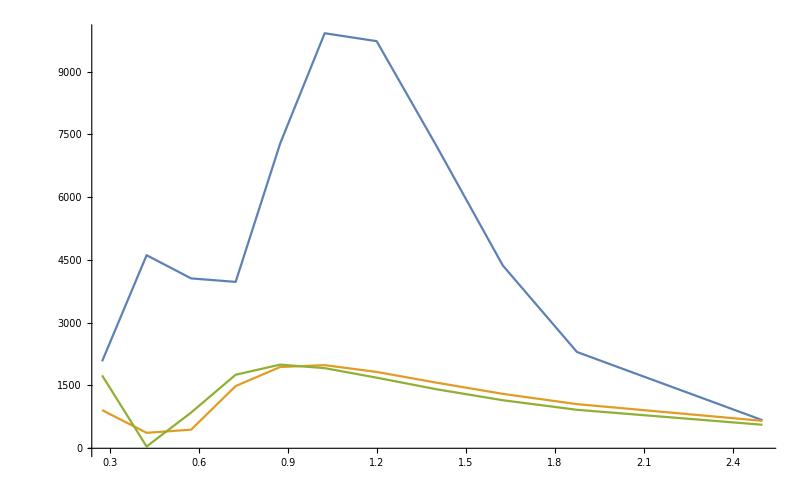

```mathematica
ListPlot[{Table[{erate[[i,1]],erate[[i,3]]/erate[[i,2]]},{i,1,Length[erate]}],Table[{erate[[i,1]],2000*Sin[2*1.27*0.600/erate[[i,1]]]^2},{i,1,Length[erate]}],Table[{erate[[i,1]],2000*Sin[10*1.27*0.11/erate[[i,1]]]^2},{i,1,Length[erate]}]},PlotRange->All,Joined->True]
```

```mathematica
Table[((eappc[[i,2]]*erate[[i,2]])/(erate[[i,3]])),{i,1,Length[eappc]}]
```

{1.03356,1.6452,1.86355,0.950855,0.664336,0.995472,1.69428,3.30646,7.09916,16.3225,0.}

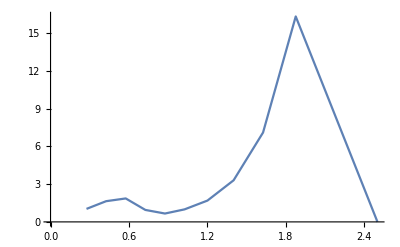

```mathematica
ListPlot[Table[{erate[[i,1]],(eappc[[i,2]]*erate[[i,2]])/(erate[[i,3]])},{i,1,Length[eappc]}],Joined->True]
```

```mathematica
ebg=Import["/home/gstenico/Desktop/nu-LED-2/ev-rates/nu-e-app-bg-LAR.dat","Data"];
```

```mathematica
ebg
```

{{0.282064,5116.28},{0.440522,8733.85},{0.585907,11007.8},{0.730819,11059.4},{0.884035,10077.5},{1.03309,9560.72},{1.20324,8062.02},{1.40754,6821.71},{1.62894,5788.11},{1.88001,4031.01},{2.4975,1860.47}}

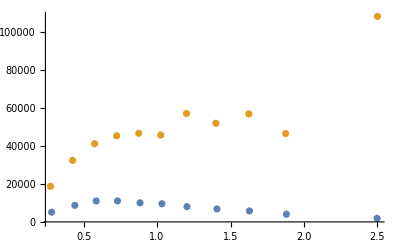

```mathematica
ListPlot[{ebg,Table[{erate[[i,1]],erate[[i,3]]},{i,1,Length[erate]}]},PlotRange->All]
```

```mathematica
Table[((ebg[[i,2]]*erate[[i,2]])/(erate[[i,3]])),{i,1,Length[ebg]}]
```

{0.0409086,0.0404435,0.0400692,0.0365442,0.0323718,0.0313439,0.028222,0.026243,0.0254154,0.0216474,0.0171821}

```mathematica
ebg2=Import["/home/gstenico/Desktop/nu-LED-2/ev-rates/nu-e-app-bg2-LAR.dat","Data"];
ebg2c=Table[{ebg2[[i,1]],(ebg2[[i+1,2]]-ebg2[[i,2]])},{i,1,Length[ebg2],2}];
```

```mathematica
Table[((ebg2c[[i,2]]*erate[[i,2]])/(erate[[i,3]])),{i,1,Length[ebg2c]}]
```

```mathematica
{0.006198277696975996,0.0031110368290175596,0.0015049457596620038,0.0006830698722538132,0.0006640372784061954,0.00016942645416794072,0.,0.,0.0006807708777114253,0.0005550618280239698,0.}
{0.0000324693,0.0000115971,0.00000513708,0.00000237088,0.00000214484,0.00000216155,0.00000162465,0.,0.,0.,0.}
```